```mathematica
w=((1+α) (c+2 c α+a (α+θ))-(1+2 α) (1+α-μ α) Subscript[c, r])/(2 (1+α) (1+2 α))
```

((1+α) (c+2 c α+a (α+θ))-(1+2 α) (1+α-α μ) c_r)/(2 (1+α) (1+2 α))

```mathematica
pm=(2 (1+α)^2 (c+2 c α+a (1+α-θ)) (-2+Subscript[τ, r])+2 (1+α)^2 (1+2 α) Subscript[c, d] (-2+Subscript[τ, r])+Subscript[τ, m] ((1+α) (c α (1+2 α)+a (4+α (8+α)))-a (4+3 α (3+α)) θ+α (1+2 α) (1+α-α μ) Subscript[c, r]-2 a (1+2 α) (1+α-θ) Subscript[τ, r]))/(2 (1+2 α) (2 (1+α)^2 (-2+Subscript[τ, r])+Subscript[τ, m] (2+α (4+α)-(1+2 α) Subscript[τ, r])))
```

(2 (1+α)^2 (c+2 c α+a (1+α-θ)) (-2+τ_r)+2 (1+α)^2 (1+2 α) c_d (-2+τ_r)+τ_m ((1+α) (c α (1+2 α)+a (4+α (8+α)))-a (4+3 α (3+α)) θ+α (1+2 α) (1+α-α μ) c_r-2 a (1+2 α) (1+α-θ) τ_r))/(2 (1+2 α) (2 (1+α)^2 (-2+τ_r)+τ_m (2+α (4+α)-(1+2 α) τ_r)))

```mathematica
pr=(-2 (1+α) (2 a α (1+α)+c (1+2 α)^2+a (3+4 α) θ)-(1+α) (1+2 α) (-1+α (-1+μ)) Subscript[c, r] (-2+Subscript[τ, m])+(c (1+α)^2 (1+2 α)+a (3+α (6+α)) (α+θ)) Subscript[τ, m]+2 α (1+α) (1+2 α) Subscript[c, d] (-1+Subscript[τ, r])+2 ((1+α) (α (a+c+a α+2 c α)+a (2+3 α) θ)-a (1+2 α) (α+θ) Subscript[τ, m]) Subscript[τ, r])/(2 (1+2 α) (2 (1+α)^2 (-2+Subscript[τ, r])+Subscript[τ, m] (2+α (4+α)-(1+2 α) Subscript[τ, r])))
```

(-2 (1+α) (2 a α (1+α)+c (1+2 α)^2+a (3+4 α) θ)-(1+α) (1+2 α) (-1+α (-1+μ)) c_r (-2+τ_m)+(c (1+α)^2 (1+2 α)+a (3+α (6+α)) (α+θ)) τ_m+2 α (1+α) (1+2 α) c_d (-1+τ_r)+2 ((1+α) (α (a+c+a α+2 c α)+a (2+3 α) θ)-a (1+2 α) (α+θ) τ_m) τ_r)/(2 (1+2 α) (2 (1+α)^2 (-2+τ_r)+τ_m (2+α (4+α)-(1+2 α) τ_r)))

```mathematica
a=20
c=2
Subscript[c, r]=1
Subscript[c, d] =0.5
θ=0.6
α=0.4
Subscript[τ, r]=0.5
Subscript[τ, m]=0.5
```

20

2

1

0.5

0.6

0.4

0.5

0.5

```mathematica
p1=Plot[{w,pm,pr},{μ,0,10},AxesLabel->{μ,价格决策},PlotLegends->Placed[{W,Pm,Pr},Center],PlotRange->{4,10}]
```

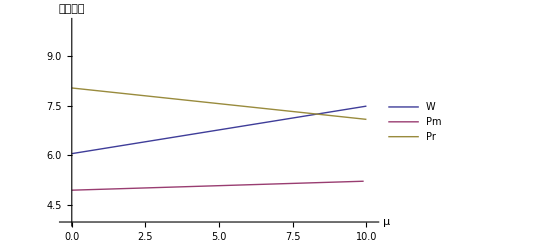

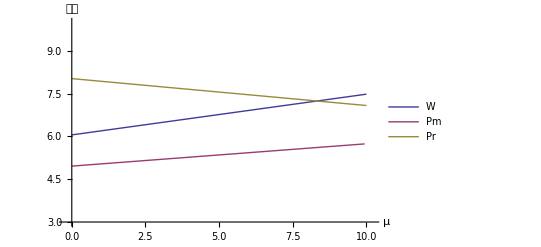

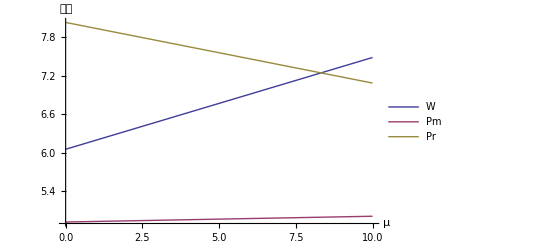

```mathematica
Plot3D[(4a b*b +6a*a*b+b*b*b)/(6a*a*a+4 a*b*b+6 *a*a*b+b*b*b),{a,0,4},{b,0,4},ColorFunction->(ColorData["TemperatureMap",#3]&)]
```

-Graphics3D-

```mathematica
Plot3D[(4a b*b +6a*a*b+b*b*b)/(6a*a*a+4 a*b*b+6 *a*a*b+b*b*b),{a,0,4},{b,0,4},ColorFunction->(ColorData[a]&)]
```

-Graphics3D-

```mathematica
,ColorFunction->(ColorData["TemperatureMap",#3]&)
```